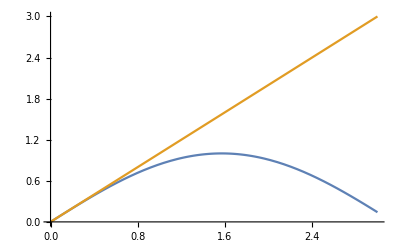

```mathematica
Plot[{Sin[x],x},{x,0,3}]
```

```mathematica
Series[Log[2,1+x],{x,0,10}]
```

x/Log[2]-x^2/(2 Log[2])+x^3/(3 Log[2])-x^4/(4 Log[2])+x^5/(5 Log[2])-x^6/(6 Log[2])+x^7/(7 Log[2])-x^8/(8 Log[2])+x^9/(9 Log[2])-x^10/(10 Log[2])+O[x]^11

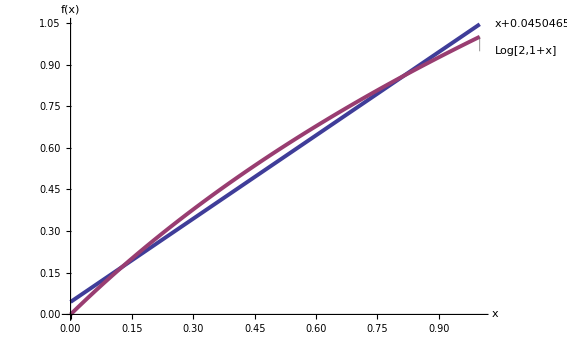

```mathematica
Plot[{x+0.0450465,Log[2,1+x]},{x,0,1},PlotTheme->"Classic",PlotLabels->{"x+0.0450465","Log[2,1+x]"},AxesLabel->{x,f[x]},PlotStyle->{Thickness[0.005]},ImageSize->{567,377}]
```

```mathematica
Export["/home/andrey/Рабочий стол/курсовая(мат. пакеты)/текст/approxLog.jpg",%4,"JPEG"]
```

/home/andrey/Рабочий стол/курсовая(мат. пакеты)/текст/approxLog.jpg

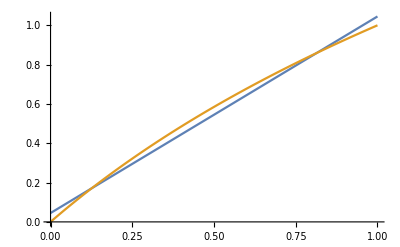

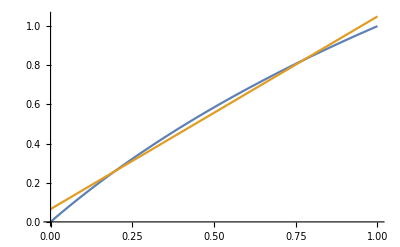

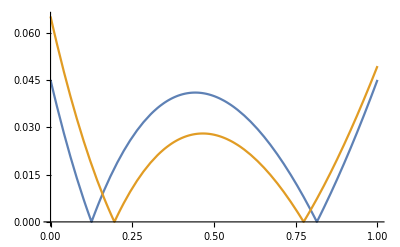

```mathematica
Plot[{x+0.0450465,Log[2,1+x]},{x,0,1}]
Plot[{Log[2,1+x],0.984256*x+0.0651765},{x,0,1}]
Plot[{Abs[x+0.0450465-Log[2,1+x]],Abs[0.984256*x+0.0651765-Log[2,1+x]]},{x,0,1}]
```

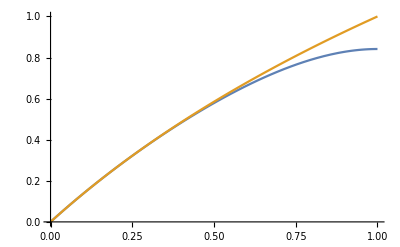

```mathematica
Plot[{x/(Log[2])-x^2/(2*Log[2])+x^3/(3*Log[2])-x^4/(4*Log[2]),Log[2,1+x]},{x,0,1}]
```

```mathematica
res=Solve[a*x^3+b*x^2+c*x+d==0,x]//FullSimplify
```

{{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)},{x→-b/(3 a)+((1+ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3))-1/(6 2^(1/3) a)(1-ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3)},{x→-b/(3 a)+((1-ⅈ √3) (-b^2+3 a c))/(3 2^(2/3) a (-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3))-1/(6 2^(1/3) a)(1+ⅈ √3) (-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3)}}

```mathematica
res[[1]]
```

{x→-b/(3 a)-(2^(1/3) (-b^2+3 a c))/(3 a (-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3))+((-2 b^3+9 a b c-27 a^2 d+√(-4 (b^2-3 a c)^3+(2 b^3-9 a b c+27 a^2 d)^2))^(1/3))/(3 2^(1/3) a)}

```mathematica
Series[Sqrt[1+x],{x,0,10}]
```

1+x/2-x^2/8+x^3/16-(5 x^4)/128+(7 x^5)/256-(21 x^6)/1024+(33 x^7)/2048-(429 x^8)/32768+(715 x^9)/65536-(2431 x^10)/262144+O[x]^11

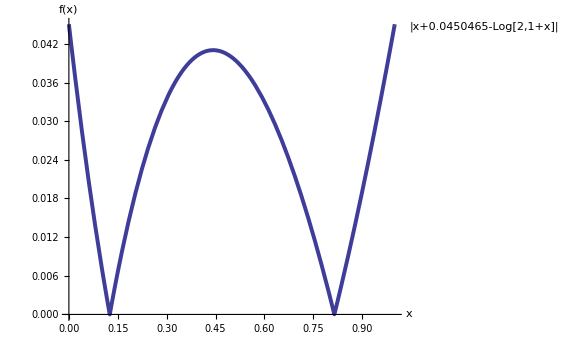

```mathematica
Plot[Abs[x+0.0450465-Log[2,1+x]],{x,0,1},PlotTheme->"Classic",PlotLabels->"|x+0.0450465-Log[2,1+x]|",AxesLabel->{x,f[x]},PlotStyle->{Thickness[0.005]},ImageSize->{567,377}]
```

```mathematica
Export["/home/andrey/Рабочий стол/курсовая(мат. пакеты)/текст/residLog.jpg",%11,"JPEG"]
```

/home/andrey/Рабочий стол/курсовая(мат. пакеты)/текст/residLog.jpg